```mathematica
ClearAll["Global`*"]
nunready=n0*Exp[-llag*t];
nready=((llag*n0)/(lcond-llag))*(Exp[-llag*t]-Exp[-lcond*t]);
ncond =1+((n0/(lcond-llag))*(((Exp[-lcond*t]*llag))-(Exp[-llag*t]*lcond)));
fx = -((n0*llag*lcond/(lcond-llag))*(((Exp[-lcond*t]))-(Exp[-llag*t])));
```

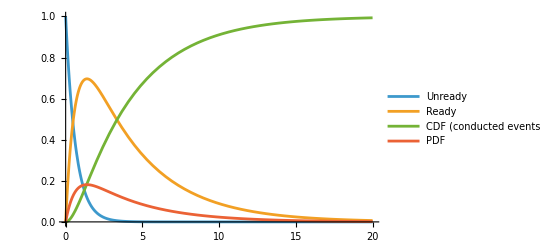

```mathematica
n0=1;
lcond=(1/3.84);
llag=(1/0.65);
Plot[{nunready,nready,ncond,fx},{t,0,20},PlotLegends->{"Unready","Ready","CDF (conducted events)","PDF"}]
```